# The N=2 characteristic polynomial

## Study the behavior of λ with q-ratio

```mathematica
matEl[n_,m_,e_,v_]:=Piecewise[{{n*e, n==m}, {Sqrt[m+1]Sqrt[m+2](-v), n-m==2}, {Sqrt[m]Sqrt[m-1](-v), n-m==-2}}];
Hmat02[n_,e_,v_]:=Table[Table[matEl[2(i-1),2(j-1),e,v],{j,1,n}],{i,1,n}];
Hmat13[n_,e_,v_]:=Table[Table[matEl[2i+1,2j+1,e,v],{j,0,n-1}],{i,0,n-1}];
```

```mathematica
boson0[n_]:=Hmat02[n,1,q];
boson1[n_]:=Hmat13[n,1,q];
function[q_,n_]:=Table[Eigenvalues[boson0[n]][[id]],{id,1,Length[Eigenvalues[boson0[n]]]}];
```

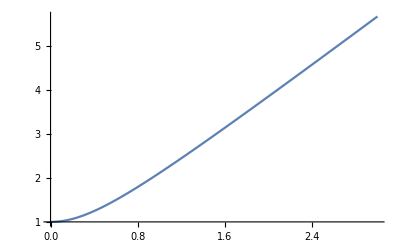

```mathematica
Plot[√(1+2 √3 q^2),{q,0,3}]
```

```mathematica
proc[n_]:=Manipulate[Plot[function[q,n][[id]],{q,0,3}],{id,1,Length[Eigenvalues[boson0[n]]],1}];
```

### The solutions λ_i of H_nwith a fixed n

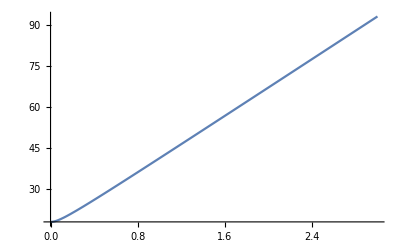
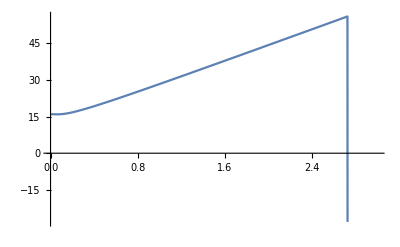
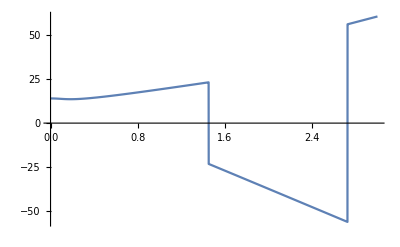
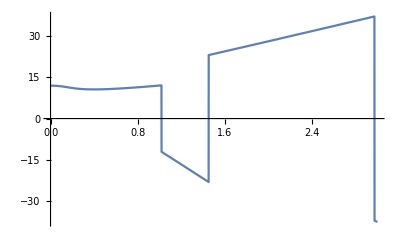
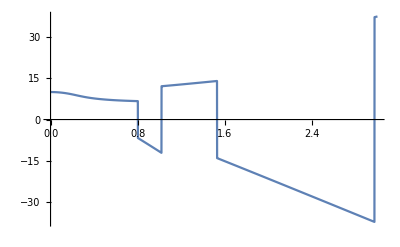
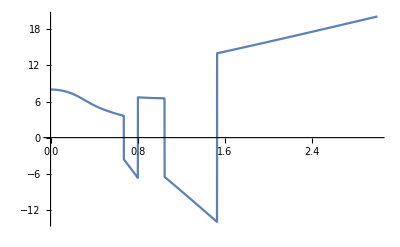
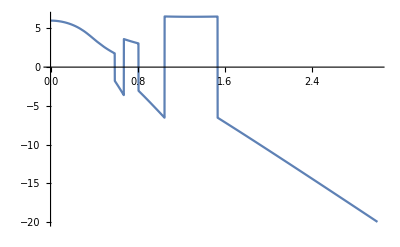
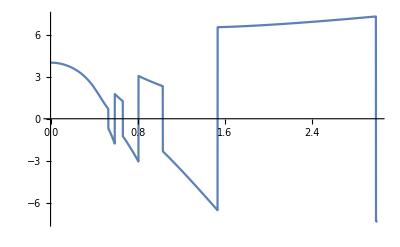

```mathematica
Table[Plot[function[q,10][[id]],{q,0,3}],{id,1,Length[Eigenvalues[boson0[10]]],1}]
```

## q=1, Numerical example: solutions

```mathematica
N[Eigenvalues[boson0[10]]/.{q->1.2}]
```

{-16.7246,-8.88007,-3.66803,-0.685819,1.88377,6.49895,12.7628,20.8926,31.526,46.3944}

```mathematica
N[Eigenvalues[boson0[9]]/.{q->1.2}]
```

{-14.4204,-7.02484,-2.34029,0.0407015,3.49194,8.99424,16.4229,26.3598,40.4759}

```mathematica
N[Eigenvalues[boson0[8]]/.{q->1.2}]
```

{-12.1576,-5.26187,-1.29381,1.03398,5.54168,12.1724,21.3362,34.6291}

```mathematica
N[Eigenvalues[boson0[7]]/.{q->1.2}]
```

{-9.94604,-3.62532,-0.512726,2.52284,8.20101,16.4901,28.8702}

```mathematica
N[Eigenvalues[boson0[6]]/.{q->1.2}]
```

{-7.79993,-2.19897,0.300783,4.6028,11.8728,23.2226}

```mathematica
f610[q_]:=Eigenvalues[boson0[10]/.{q->1.2}][[6]];
f69[q_]:=Eigenvalues[boson0[9]/.{q->1.2}][[6]];
f68[q_]:=Eigenvalues[boson0[8]/.{q->1.2}][[6]];
f67[q_]:=Eigenvalues[boson0[7]/.{q->1.2}][[6]];
f66[q_]:=Eigenvalues[boson0[6]/.{q->1.2}][[6]];
```

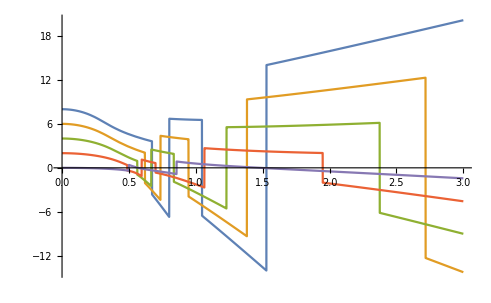

```mathematica
Plot[{f610[q],f69[q],f68[q],f67[q],f66[q]},{q,0,3}]
```

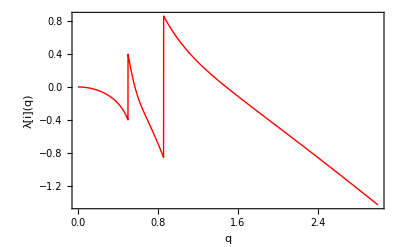

```mathematica
Plot[function[q,6][[6]],{q,0,3},Axes -> False, Frame -> True, 
 PlotRange -> {Full, Full}, PlotStyle->{Red,Thick},
 FrameLabel -> {"q","λ[i](q)"}, 
 LabelStyle -> {20, Bold, Black, FontFamily -> "Times New Roman"}]
```

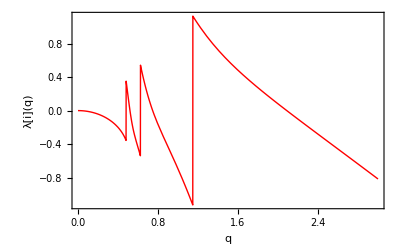

```mathematica
Plot[function[q,8][[8]],{q,0,3}, Axes -> False, Frame -> True, 
 PlotRange -> {Full, Full}, PlotStyle->{Red,Thick},
 FrameLabel -> {"q","λ[i](q)"}, 
 LabelStyle -> {20, Bold, Black, FontFamily -> "Times New Roman"}]
```